12

12

8.36639+3.50978/r

| Estimate | Standard Error | t-Statistic | P-Value
Ms | 2.7888 | 0.385131 | 7.24117 | 0.0000888132
Mdm | 2.7888 | 0.385131 | 7.24117 | 0.0000888132
as | 2.7888 | 0.385131 | 7.24117 | 0.0000888132
adm | 3.50978 | 1.83034 | 1.91755 | 0.0914604

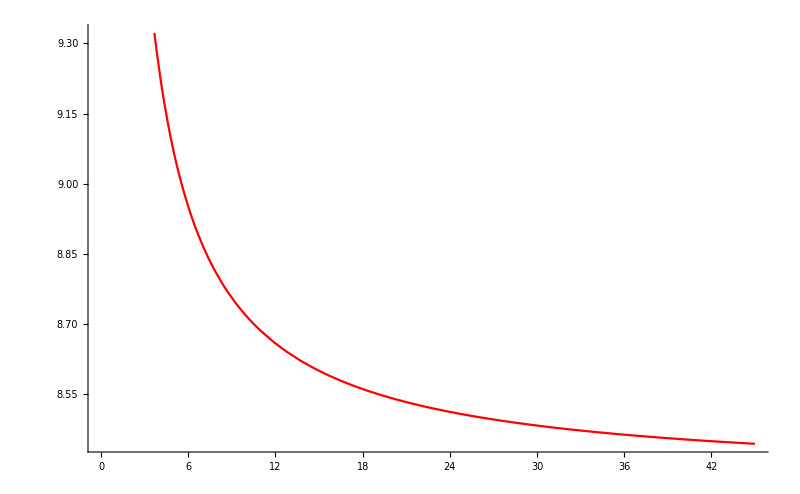

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["sigma.dat"];
L=Length[data]
12
fit=NonlinearModelFit[ data,Ms+Mdm+as+adm/r,{Ms,Mdm,as,adm},r,MaxIterations->1000];
fit["BestFit"]
fit["ParameterTable"]
Plot[fit[r],{r,0,45},PlotStyle->Red,Epilog->Point[data],ImageSize->800]
```